### Task #1

```mathematica
U[r_]:=A/r^12-B/r^6
```

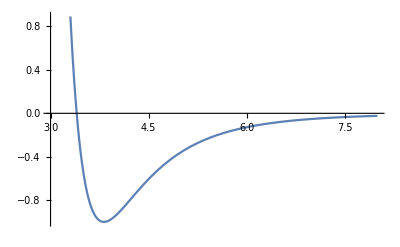

```mathematica
ϵ=0.997;  σ=3.4;
A=4ϵ σ^12;  B=4 ϵ σ^6;
Plot[U[r],{r,3,8}]
```

### Task #2

```mathematica
(*方案一：使用 Solve*)root=Solve[{D[U[r],r]==0,r>0},r];
(*使用Solve求解多项式方程，符号计算范畴；然而容易引发警告；*)

root[[1]]
U[r]/.root[[1]]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{r→3.81637}

-0.997

```mathematica
(*方案二：使用 NSolve*)root=NSolve[{D[U[r],r]==0,r>0},r]  (*使用NSolve代替Solve*)
U[r]/.root[[1]]
```

{{r→3.81637}}

-0.997

### Task #3

```mathematica
Minimize[U[x],x]
```

{-0.997,{x→-3.81637}}

```mathematica
FindMinimum[U[r],{r,5}]
```

{-0.997,{r→3.81637}}